# Taggar/GERF

GERF expansion technique in Mathematica

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"GERFSolve.nb"DocumentationEnglishReferencePagesSymbolsGERFSolve.nb

"Tutorials"

"Kernel"

"GERF.wl"KernelGERF.wl

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

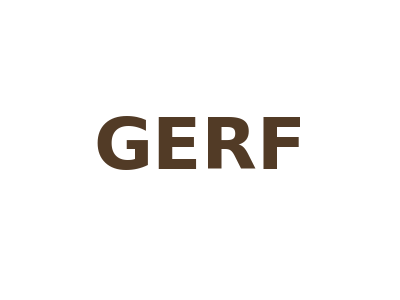

### Basic Description

The well known Generalized Rational Exponential Function (GERF) method has been used on various equations to obtain their analytic travelling wave solutions. This paclet introduces GERFSolve function that solves given nonlinear partial differential equation using this expansion technique.

### Details

The paclet provides a function to solve NLPDEs using GERF method, and offers various customisations such as using different forms of ansatz or wave transformations.

To read more about the GERF method, one should see https://doi.org/10.1016/j.rinp.2023.106298.

### Primary Context

Taggar`GERF`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["Taggar`GERF`"];
```

### Basic Examples

This is the Burgers' equation in (1+1)-dimensions:

```mathematica
burgers=D[u[x,t], t]+u[x,t]D[u[x,t], x]-ν D[u[x,t], x,x]==0
```

u^(0,1)[x,t]+u[x,t] u^(1,0)[x,t]-ν u^(2,0)[x,t]==0

Solve it using GERF method:

```mathematica
GERFSolve[burgers,u[x,t]]
```

{u[x,t]→𝒜_0,u[x,t]→𝒜_0+((ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_1)/(-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))),u[x,t]→((-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_-1)/(ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1)))+𝒜_0,u[x,t]→((-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_-1)/(ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1)))+((ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_-1)/(-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1)))+𝒜_0}

Obtain the solution sets as well:

```mathematica
sols=GERFSolve[burgers,u[x,t],"OutputMode"->"Both"]
```

{{{𝒜_-1→0,𝒜_1→0},u[x,t]→𝒜_0},{{ν→(ⅈ 𝒜_1)/(2 𝒞_1),𝒜_-1→0,𝒞_2→-𝒜_0 𝒞_1},u[x,t]→𝒜_0+((ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_1)/(-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1)))},{{ν→(ⅈ 𝒜_-1)/(2 𝒞_1),𝒜_1→0,𝒞_2→-𝒜_0 𝒞_1},u[x,t]→((-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_-1)/(ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1)))+𝒜_0},{{ν→(ⅈ 𝒜_-1)/(2 𝒞_1),𝒜_1→𝒜_-1,𝒞_2→-𝒜_0 𝒞_1},u[x,t]→((-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_-1)/(ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1)))+((ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))) 𝒜_-1)/(-ⅇ^(-ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1))+ⅇ^(ⅈ (x 𝒞_1-t 𝒜_0 𝒞_1)))+𝒜_0}}

Verify that the solutions are valid:

```mathematica
pick=sols[[2]];
burgers/. u->Function[{x,t},pick[[2,2]]]
```

True

Another example, Calogero–Bogoyavlenskii–Schiff equation in (2+1)-dimensions:

```mathematica
cbs=D[u[x,y,t], x,t]+4 D[u[x,y,t], x]D[u[x,y,t], x,y]+2 D[u[x,y,t], x,x]D[u[x,y,t], y]+ D[u[x,y,t], x,x,x,y]==0;
```

Solve it:

```mathematica
sols=GERFSolve[cbs,u[x,y,t]]
```

{u[x,y,t]→((-ⅇ^(-ⅈ (y 𝒞_2+t 𝒞_3))+ⅇ^(ⅈ (y 𝒞_2+t 𝒞_3))) 𝒜_-1)/(ⅇ^(-ⅈ (y 𝒞_2+t 𝒞_3))+ⅇ^(ⅈ (y 𝒞_2+t 𝒞_3)))+𝒜_0+((ⅇ^(-ⅈ (y 𝒞_2+t 𝒞_3))+ⅇ^(ⅈ (y 𝒞_2+t 𝒞_3))) 𝒜_1)/(-ⅇ^(-ⅈ (y 𝒞_2+t 𝒞_3))+ⅇ^(ⅈ (y 𝒞_2+t 𝒞_3))),u[x,y,t]→𝒜_0,u[x,y,t]→((-ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2)) 𝒜_-1)/(ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2))+𝒜_0+((ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2)) 𝒜_1)/(-ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2)),u[x,y,t]→((-ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1)) 𝒜_-1)/(ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1))+𝒜_0+((ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1)) 𝒜_1)/(-ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1)),u[x,y,t]→𝒜_0+(2 ⅈ (ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))) 𝒞_1)/(-ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))),u[x,y,t]→𝒜_0+(2 ⅈ (-ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))) 𝒞_1)/(ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+4 t 𝒞_1^2 𝒞_2))),u[x,y,t]→𝒜_0+(2 ⅈ (-ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2))) 𝒞_1)/(ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2)))+(2 ⅈ (ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2))) 𝒞_1)/(-ⅇ^(-ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2))+ⅇ^(ⅈ (x 𝒞_1+y 𝒞_2+16 t 𝒞_1^2 𝒞_2))),u[x,y,t]→((-ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2)) 𝒜_-1)/(ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2))+((ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2)) 𝒜_-1)/(-ⅇ^(-ⅈ y 𝒞_2)+ⅇ^(ⅈ y 𝒞_2))+𝒜_0,u[x,y,t]→((-ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1)) 𝒜_-1)/(ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1))+((ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1)) 𝒜_-1)/(-ⅇ^(-ⅈ x 𝒞_1)+ⅇ^(ⅈ x 𝒞_1))+𝒜_0}

Verification:

```mathematica
Table[cbs/. u->Function[{x,y,t},pick[[i,2]]],{i,Length@sols}]
```

{True,True,True,True,True,True,True,True,True}

### Scope

Use given constants for the wave transformation:

```mathematica
GERFSolve[burgers,u[x,t],"WaveConstants"->{a,b}]//Simplify
```

{u[x,t]→𝒜_0,u[x,t]→𝒜_0+((ⅇ^(2 ⅈ a x)+ⅇ^(2 ⅈ a t 𝒜_0)) 𝒜_1)/(ⅇ^(2 ⅈ a x)-ⅇ^(2 ⅈ a t 𝒜_0)),u[x,t]→((ⅇ^(2 ⅈ a x)-ⅇ^(2 ⅈ a t 𝒜_0)) 𝒜_-1)/(ⅇ^(2 ⅈ a x)+ⅇ^(2 ⅈ a t 𝒜_0))+𝒜_0,u[x,t]→(2 (ⅇ^(4 ⅈ a x)+ⅇ^(4 ⅈ a t 𝒜_0)) 𝒜_-1)/(ⅇ^(4 ⅈ a x)-ⅇ^(4 ⅈ a t 𝒜_0))+𝒜_0}

## Source & Additional Information

### Creator

Naman T.

### Source Control Repository

https://github.com/UserName/MyPaclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

nonlinear partial differential equations

expansion techniques

exact solutions

GERF method

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

14.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.